```mathematica
(* 
The various conditions used below are
GICPF   ((R) β)^(1/ρ) < 𝔊
GICTBS  ((R) β)^(1/ρ) < Γ = 𝔊/(1-℧)
RIC     ((R) β)^(1/ρ) < (R)
*)
```

```mathematica
(* The appendix now proves that whenever FHWC-TBS fails, ÞΓ ≤ ÞRtn so which implies that ϖ>0 which implies Π>1 which implies that there is a solution *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

βMaxWhereRICHoldsExactly=(R)^(ρ-1);ϑMinWhereRICHoldsExactly=(βMaxWhereRICHoldsExactly)^-1-1;
βMaxWhereGICPFHoldsExactly=𝔊^ρ/(R); 
ϑMinWhereGICPFHoldsExactly=(βMaxWhereGICPFHoldsExactly)^-1-1;
βMaxWhereGICTBSHoldsExactly=Γ^ρ/(R); 
ϑMinWhereGICTBSHoldsExactly=(βMaxWhereGICTBSHoldsExactly)^-1-1;
βMaxWhereGICFailsEnoughToPreventExistenceOfTarget = ((1-℧)(R))^(ρ-1);
ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget=(βMaxWhereGICFailsEnoughToPreventExistenceOfTarget)^-1-1;

<<ManipulatePrepare.m;
```

```mathematica
Clear[α,℧,ϑ];
𝔊=(1-α ℧)(R);

ℛ
```

(1. (1-℧))/(1-α ℧)

```mathematica
κ
```

1-0.985329 (1/(1+ϑ))^0.5

```mathematica
α=1;(* This is the cusp case in which FHWC-TBS exactly fails *)
```

```mathematica
℧Min=0.00001;
℧Max=0.02;
```

```mathematica
{βTop,βBot}=βMaxWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ -> {℧Min,℧Max}
```

{1.02999,1.0094}

```mathematica
{ϑBot,ϑTop}=ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ -> {℧Min,℧Max}
```

{-0.0291165,-0.00931246}

```mathematica
ℛ
```

1.

```mathematica
α=1
```

1

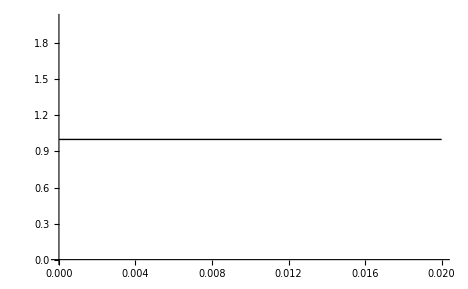

```mathematica
Plot[ℛ /. ϑ -> (ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ -> ℧Plot),{℧Plot,℧Min,℧Max}]
```

```mathematica
Π /. ϑ -> (ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ ->℧Min) /. ℧ -> ℧Min
```

1.41422

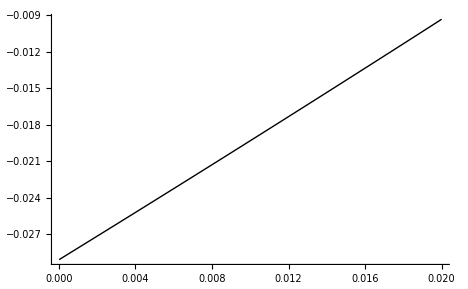

```mathematica
Plot[(ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ -> ℧Plot),{℧Plot,℧Min,℧Max}]
```

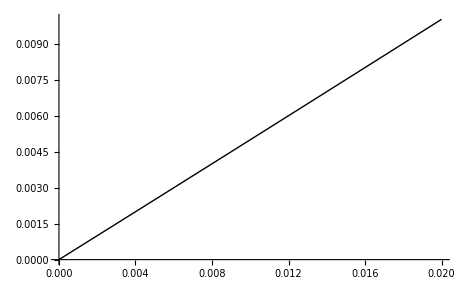

```mathematica
Plot[κ /. ϑ -> (ϑMinWhereGICFailsEnoughToPreventExistenceOfTarget /. ℧ -> ℧Plot),{℧Plot,℧Min,℧Max}]
```

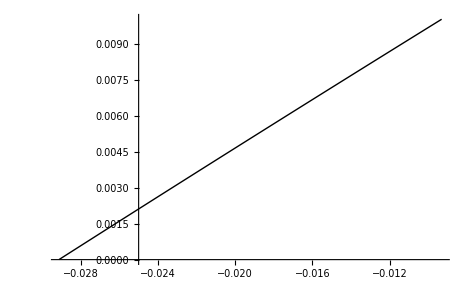

```mathematica
Plot[κ /. ϑ -> ϑPlot,{ϑPlot,ϑBot,ϑTop}]
```

```mathematica
κ /. ϑ->{ϑBot,ϑTop}
```

{5.00001×10^-6,0.0100505}

```mathematica
Plot[κ /.
```

```mathematica
ℛ
```

1.

```mathematica
Π
```

14.1421 (-0.995+1.02033/(1/(1-0.005 α))^2.)^0.5

```mathematica
(1-℧)^(1-1/ρ)
```

0.997497

```mathematica
?κ
```

κ

Global`

CreateUUID["Info-"]

False

False

False

```mathematica
κ
```

0.00503782

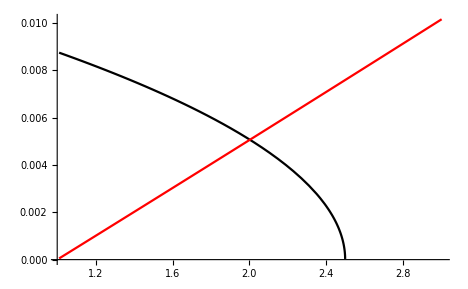

```mathematica
Plot[{κ Π ℛ /. α -> αPlot,ℛ-1 /. α -> αPlot},{αPlot,1.01,3},PlotStyle->{Black,Red}]
```

```mathematica
β
```

1.11108 (1-0.005 α)^2.

```mathematica
κ
```

1-1.00503 ((1-0.005 α)^2.)^0.5

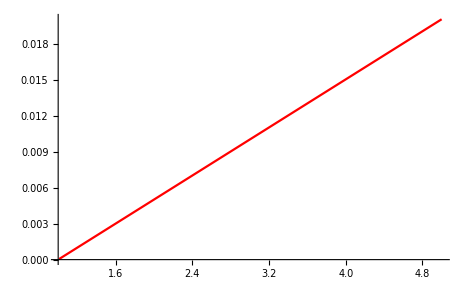

```mathematica
Plot[{κ /. α->αPlot},{αPlot,1.01,5},PlotStyle->{Black,Red}]
```

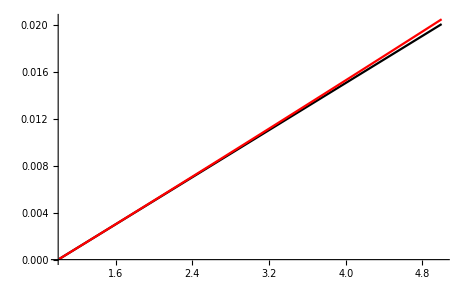

```mathematica
Plot[{κ /. α->αPlot,(R)/Γ-1 /. α->αPlot},{αPlot,1.01,5},PlotStyle->{Black,Red}]
```

```mathematica
ϑMin
```

-0.0907272